(0+1)D boost-invariant spin hydrodynamics
 GREEN CELLS CAN BE EVALUATED QUITE AUTOMATICALLY, THE REST IS MAY NOT WORK PROPERLY IF NOT CHOSE PROPER IC
 IN section II solutionN=2 is for choosing problematic IC (then also red cells can be evaluated), solutionN=1  is IC which is OK
 author: Radoslaw Ryblewski  (Radoslaw.Ryblewski@ifj.edu.pl), Natalia Łygan, Wojciech Florkowski, Zbigniew Drogosz

MaTeX package

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:\\Program Files\\MiKteX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files (x86)\\gs\\gs10.04.0\\bin\\gswin32c.exe" ]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Program Files\MiKteX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files (x86)\gs\gs10.04.0\bin\gswin32c.exe}

```mathematica
<<MaTeX`
```

```mathematica
MaTeX[x^2+5-7x==0]
```

-Graphics-

```mathematica
textstyle={FontFamily-> "revtex4-1",FontSize->16,Black};
framestyle={FontFamily-> "revtex4-1",FontSize->10,Black};
MaTeX[x^2+5-7x==0]
```

-Graphics-

Setting options for Graphics

```mathematica
(* set options common for all plots, logplots etc. *)
SetOptions[{Plot,LogLogPlot,LogPlot},
{LabelStyle->{FontSize->14,Darker[Black,0.1], Plain},PlotRange->All,Frame->True,Axes->False,ImageSize->500,FrameStyle ->Directive[14]}];

style1=Directive[Red,Thickness[0.006]];
style2= Directive[Black,Thickness[0.004],Dashed];
style3=Directive[Black,Thickness[0.006],Dotted];
style4=Directive[Blue,Thickness[0.006]];
style40=Directive[Blue,Thickness[0.006],Dashed];

style01=Directive[Lighter[Blue,0.5],Thickness[0.006]];
style02=Directive[Lighter[Green,0.5],Thickness[0.006]];
style03=Directive[Lighter[Red,0.5],Thickness[0.006]];
style010=Directive[Darker[Blue,0.5],Thickness[0.004],Dashed];
style020=Directive[Darker[Green,0.5],Thickness[0.004],Dashed];
style030=Directive[Darker[Red,0.5],Thickness[0.004],Dashed];
```

```mathematica
(* <<MaTeX` *)
```

I. Equation of state

```mathematica
(* formulas taken from the draft "Perfect spin hydrodynamics for Bjorken flow geometry" *)
(* g is introduced just to have more readable epressions *)
g=1/(2 π^2) ;
𝔖=√(3/4);

nn[T_,m_]:=g T^3 (m/T)^2 BesselK[2,m/T] ;

en[T_,m_]:=g T^4 (m/T)^2 ((m/T) BesselK[3,m/T] - BesselK[2,m/T]); (*** błąd, wcześniej było: ((m/T) BesselK[1,m/T] +3 BesselK[2,m/T]) ***)
pn[T_,m_]:=T nn[T,m] ;
```

```mathematica
(* charge density *)
n0[T_,μ_,m_]:=4 Sinh[μ/T] nn[T,m] ;
n2k[T_,μ_,m_,k2_]:=-4  Sinh[μ/T] g  𝔖^2/3 T^3 (m/T) BesselK[3,m/T]k2 ;
n2w[T_,μ_,m_,w2_]:=-4  Sinh[μ/T] g  𝔖^2/(2 3)T^3 (m/T)( (m/T)BesselK[2,m/T]+2BesselK[3,m/T])w2 ;
nb[T_,μ_,m_,k2_,w2_]:=n0[T,μ,m]+n2k[T,μ,m,k2]+n2w[T,μ,m,w2]
```

```mathematica
(* energy density *)
e0[T_,μ_,m_]:=4 Cosh[μ/T] en[T,m] ;
e2k[T_,μ_,m_,k2_]:=-4  Cosh[μ/T] g  𝔖^2/3 T^4 (m/T)( (m/T)BesselK[2,m/T]+5BesselK[3,m/T])k2 ;
e2w[T_,μ_,m_,w2_]:=-4  Cosh[μ/T] g  𝔖^2/(2 3)T^4 (m/T)( (m/T)BesselK[2,m/T]+((m/T)^2+10)BesselK[3,m/T])w2 ;
eb[T_,μ_,m_,k2_,w2_]:=e0[T,μ,m]+e2k[T,μ,m,k2]+e2w[T,μ,m,w2]
```

```mathematica
(* pressure *)
p0[T_,μ_,m_]:=4 Cosh[μ/T] pn[T,m]  ;
p2k[T_,μ_,m_,k2_]:=-4  Cosh[μ/T] g  (2 𝔖^2)/3 T^4 (m/T)( BesselK[3,m/T])k2 ;
p2w[T_,μ_,m_,w2_]:=-4  Cosh[μ/T] g  𝔖^2/(2 3)T^4 (m/T)( (m/T)BesselK[2,m/T]+4BesselK[3,m/T])w2 ;
pb[T_,μ_,m_,k2_,w2_]:=p0[T,μ,m]+p2k[T,μ,m,k2]+p2w[T,μ,m,w2]
ps[T_,μ_,m_]:= -4  Cosh[μ/T] g  𝔖^2/3 T^4 (m/T)( BesselK[3,m/T])
```

```mathematica
(* spin density *)
a1[T_,μ_,m_]:=4 Cosh[μ/T](g 𝔖^2)/3 T^3 m/T(m/T BesselK[2,m/T]+2 BesselK[3,m/T]) ;
a2[T_,μ_,m_]:=4 Cosh[μ/T](2g 𝔖^2)/3 T^3( m/T)^2 BesselK[4,m/T] ;
a3[T_,μ_,m_]:=-4 Cosh[μ/T](2g 𝔖^2)/3 T^3 m/T BesselK[3,m/T] ;
a[T_,μ_,m_]:=a1[T,μ,m]-1/2 a2[T,μ,m]-a3[T,μ,m]//FullSimplify
```

II. Initial conditions (Cxi=0.1 -> 0.0; Cyi=0.1 -> 0.0;)

```mathematica
solutionN=4;
```

```mathematica
(* before solving EOMs, all variables are transformed to fermi using the rule: 1 fm/c = 5.0677 1/GeV *)
hbarc=0.1973269631;

(* initial conditions are chosen same as in arXiv:1901.09655 [hep-ph] *)
(* mass of Lamda particle *)
M=(1.116 (* GeV *))/hbarc;(* fm^-1 *)

(* initial and final values for time integration *)
τi=1.0; (* fm *)
τf=10.0;(* fm *)

(* initial values of temperature and chemical potential *)
Ti=(0.155 (* GeV *))/hbarc; (* fm^-1 *)

μi=(0.800 (* GeV *))/hbarc; (* fm^-1 *) 

(*λi=λ0;*)
```

```mathematica
(* initial values of spin coefficients;  BY DEFAULT solutionN = 1 
other values of solutionN are used by me only for conveniently producing 
other sets of solutions for comparisons *)
Switch[solutionN,
1,{ 
CkZi=0.1;
CwZi=0.1; 
Ckxi=0.1;
Ckyi=0.1;
Cwxi=0.1;
Cwyi=0.1;
},
2,{ 
CkZi=0.25;
CwZi=0.25;
Ckxi=0.25;
Ckyi=0.25;
Cwxi=0.25;
Cwyi=0.25;
},
3,{ 
CkZi=0.5;
CwZi=0.5;
Ckxi=0.5;
Ckyi=0.5;
Cwxi=0.5;
Cwyi=0.5;
},
4,{ 
CkZi=0.75;
CwZi=0.75;
Ckxi=0.75;
Ckyi=0.75;
Cwxi=0.75;
Cwyi=0.75;
},
5,{ 
CkZi=1.;
CwZi=1.;
Ckxi=1.;
Ckyi=1.;
Cwxi=1.;
Cwyi=1.;
},
6,{ 
CkZi=1.25;
CwZi=1.25;
Ckxi=1.25;
Ckyi=1.25;
Cwxi=1.25;
Cwyi=1.25;
}
]
```

{Null}

III. Solving EOM (1. Longitudinal polarization)

```mathematica
(* Solution0 contains the Bjorken solution for T and μ without contributions from spin; I use it as a line of reference *)
Solution0=NDSolve[{
D[nb[T[τ],μ[τ],M,0,0],τ]+nb[T[τ],μ[τ],M,0,0]/τ==0,
D[eb[T[τ],μ[τ],M,0,0],τ]+(eb[T[τ],μ[τ],M,0,0]+pb[T[τ],μ[τ],M,0,0])/τ==0,
T[τi]==Ti,
μ[τi]==μi
},{T,μ},{τ,τi,τf}, Method->Automatic][[1]];
Ts0=Solution0[[1,2]];
μs0=Solution0[[2,2]];
```

```mathematica
(* SolutionFull contains the Bjorken solution for CkZ and CwZ as well as T and μ with 2nd order contributions from spin *)
SolutionFull=NDSolve[{
D[nb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2],τ]+nb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2]/τ==0,
D[eb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2],τ]+1/τ(eb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2]+pb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2])+ps[T[τ],μ[τ],M]/τ(CkZ[τ]^2+CwZ[τ]^2)==0,
D[CkZ[τ],τ]==-1/a[T[τ],μ[τ],M](D[a[T[τ],μ[τ],M],τ]+a[T[τ],μ[τ],M]/τ)CkZ[τ],
D[CwZ[τ],τ]==-1/a1[T[τ],μ[τ],M](D[a1[T[τ],μ[τ],M],τ]+a1[T[τ],μ[τ],M]/τ)CwZ[τ],
T[τi]==Ti,
μ[τi]==μi,
CkZ[τi]==CkZi,
CwZ[τi]==CwZi
},{T,μ,CkZ,CwZ},{τ,τi,τf}, Method->{"EquationSimplification"->"Residual"}][[1]];

(* here I pick up solutions from SolutionFull, suffix _s stands for solution *)
Ts=SolutionFull[[1,2]];
μs=SolutionFull[[2,2]]; 
CkZs=SolutionFull[[3,2]]; 
CwZs=SolutionFull[[4,2]];

(* here using solutionN I pick up various solutions from SolutionFull to make comparisons *)
Switch[solutionN,
1,{
Ts1=SolutionFull[[1,2]];
μs1=SolutionFull[[2,2]]; 
CkZs1=SolutionFull[[3,2]]; 
CwZs1=SolutionFull[[4,2]]; },
2,{
Ts2=SolutionFull[[1,2]];
μs2=SolutionFull[[2,2]]; 
CkZs2=SolutionFull[[3,2]]; 
CwZs2=SolutionFull[[4,2]]; } ,
3,{
Ts3=SolutionFull[[1,2]];
μs3=SolutionFull[[2,2]]; 
CkZs3=SolutionFull[[3,2]]; 
CwZs3=SolutionFull[[4,2]]; } ,
4,{
Ts4=SolutionFull[[1,2]];
μs4=SolutionFull[[2,2]]; 
CkZs4=SolutionFull[[3,2]]; 
CwZs4=SolutionFull[[4,2]]; } ,
5,{
Ts5=SolutionFull[[1,2]];
μs5=SolutionFull[[2,2]]; 
CkZs5=SolutionFull[[3,2]]; 
CwZs5=SolutionFull[[4,2]]; },
6,{
Ts6=SolutionFull[[1,2]];
μs6=SolutionFull[[2,2]]; 
CkZs6=SolutionFull[[3,2]]; 
CwZs6=SolutionFull[[4,2]]; } 
];



(* solution for linear expansion in Subscript[ω, μν] "Spin polarization evolution in a boost invariant hydrodynamical background" *)
SolutionNF=NDSolve[{
D[nb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2],τ]+nb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2]/τ==0,
D[eb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2],τ]+(eb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2]+pb[T[τ],μ[τ],M,-CkZ[τ]^2,-CwZ[τ]^2])/τ==0,D[CkZ[τ],τ]==-1/a[T[τ],μ[τ],M](D[a[T[τ],μ[τ],M],τ]+a[T[τ],μ[τ],M]/τ)CkZ[τ],
D[CwZ[τ],τ]==-1/a1[T[τ],μ[τ],M](D[a1[T[τ],μ[τ],M],τ]+a1[T[τ],μ[τ],M]/τ)CwZ[τ],

T[τi]==Ti,
μ[τi]==μi,
CkZ[τi]==CkZi,
CwZ[τi]==CwZi
},{T,μ,CkZ,CwZ},{τ,τi,τf}, Method->{"EquationSimplification"->"Residual"}][[1]];
Tsnf=SolutionNF[[1,2]];
μsnf=SolutionNF[[2,2]] ;
CkZsnf=SolutionNF[[3,2]];
CwZsnf=SolutionNF[[4,2]];

Switch[solutionN,
1,{
Ts1=SolutionNF[[1,2]];
μs1=SolutionNF[[2,2]]; 
CkZs1=SolutionNF[[3,2]]; 
CwZs1=SolutionNF[[4,2]]; },
2,{
Ts1=SolutionNF[[1,2]];
μs1=SolutionNF[[2,2]]; 
CkZs1=SolutionNF[[3,2]]; 
CwZs1=SolutionNF[[4,2]]; },
3,{
Ts3=SolutionNF[[1,2]];
μs3=SolutionNF[[2,2]]; 
CkZs3=SolutionNF[[3,2]]; 
CwZs3=SolutionNF[[4,2]]; },
4,{
Ts4=SolutionNF[[1,2]];
μs4=SolutionNF[[2,2]]; 
CkZs4=SolutionNF[[3,2]]; 
CwZs4=SolutionNF[[4,2]]; },
5,{
Ts5=SolutionNF[[1,2]];
μs5=SolutionNF[[2,2]]; 
CkZs5=SolutionNF[[3,2]]; 
CwZs5=SolutionNF[[4,2]]; },
6,{
Ts6=SolutionNF[[1,2]];
μs6=SolutionNF[[2,2]]; 
CkZs6=SolutionNF[[3,2]]; 
CwZs6=SolutionNF[[4,2]]; }
];
```

```mathematica
(* for plotting I use τm instead of τf, since sometimes the NDSolve does not reach τf *)
τm=Ts[[1,1,2]];
```

IV . Plot Solutions (1. Longitudinal polarization)

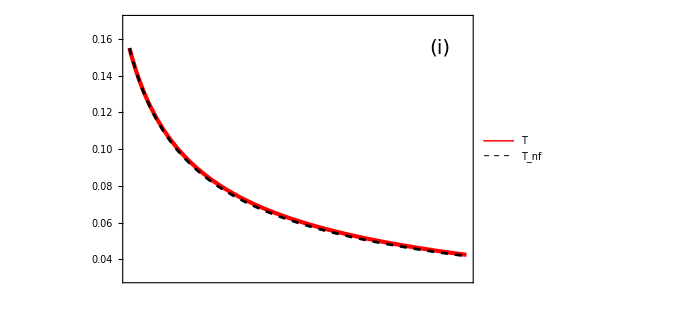

```mathematica
AL=Plot[{Ts[τ]hbarc,Ts0[τ]hbarc},{τ,τi,τm},PlotRange->{{1,10},{0.03,0.17}},
BaseStyle->textstyle,PlotStyle->{style1,style2},
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{{{0.04,"0.04",0.03},{0.035,"",0.01},{0.045,"",0.01},{0.05,"",0.015},{0.055,"",0.01},{0.06,"0.06",0.03},{0.065,"",0.01},{0.07,"",0.015},{0.075,"",0.01},{0.08,"0.08",0.03},{0.085,"",0.01},{0.09,"",0.015},{0.095,"",0.01},{0.10,"0.10",0.03},{0.105,"",0.01},{0.11,"",0.015},{0.115,"",0.01},{0.12,"0.12",0.03},{0.125,"",0.01},{0.13,"",0.015},{0.135,"",0.01},{0.14,"0.14",0.03},{0.145,"",0.01},{0.15,"",0.015},{0.155,"",0.01},{0.16,"0.16",0.03},{0.165,"",0.01}},None},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}}}},
Epilog->{Text[Style["(i)",FontSize->20],{9.3,0.155}],Rotate[Text[Style["T [GeV]",FontSize->19],{-0.3,0.1}],90Degree]},
PlotLegends->Placed[LineLegend[{"T","T_nf"},LabelStyle->textstyle],Scaled[{0.85,0.35}]],PlotRangeClipping->False,ImagePadding->{{70,70},{70,10}}]
```

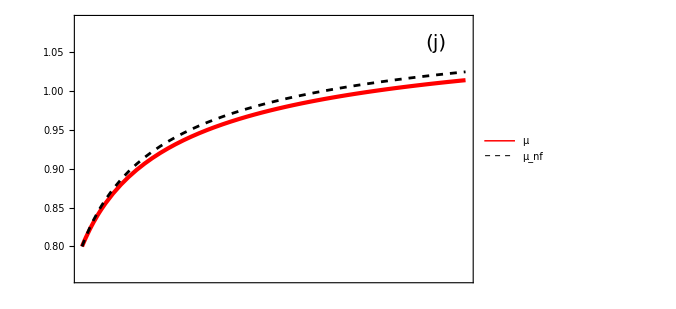

```mathematica
BL=Plot[{μs[τ]hbarc,μs0[τ]hbarc},{τ,τi,τm},PlotRange->{{1,10},{0.76,1.09}},
PlotStyle->{style1,style2},BaseStyle->textstyle,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{0.77,"",0.015},{0.78,"",0.015},{0.79,"",0.015},{0.80,"0.80",0.03},{0.81,"",0.015},{0.82,"",0.015},{0.83,"",0.015},{0.84,"",0.015},{0.85,"0.85",0.03},{0.86,"",0.015},{0.87,"",0.015},{0.88,"",0.015},{0.89,"",0.015},{0.9,"0.90",0.03},{0.91,"",0.015},{0.92,"",0.015},{0.93,"",0.015},{0.94,"",0.015},{0.95,"0.95",0.03},{0.96,"",0.015},{0.97,"",0.015},{0.98,"",0.015},{0.99,"",0.015},{1,"1.00",0.03},{1.01,"",0.015},{1.02,"",0.015},{1.03,"",0.015},{1.04,"",0.015},{1.05,"1.05",0.03},{1.06,"",0.015},{1.07,"",0.015},{1.08,"",0.015},{1.10,"1.10",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}}}},
Epilog->{Text[Style["(j)",FontSize->20],{9.3,1.06}],Rotate[Text[Style["μ [GeV]",FontSize->19],{11.4,0.94}],-90Degree]},
PlotLegends->Placed[LineLegend[{"μ","μ_nf"},LabelStyle->textstyle],Scaled[{0.17,0.8}]],PlotRangeClipping->False,ImagePadding->{{70,70},{70,10}}]
```

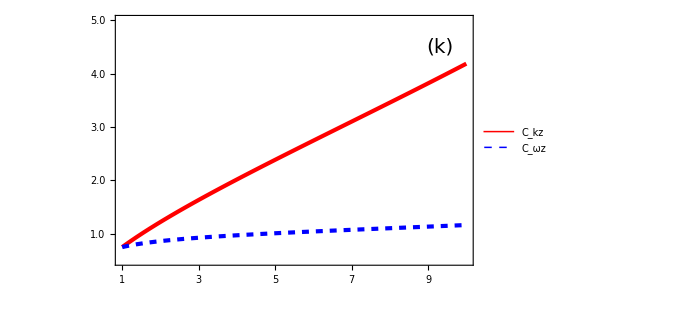

```mathematica
CL=Plot[{CkZs[τ],CwZs[τ]} ,{τ,τi,τm},PlotRange->{{1,10},{0.5,5.0}},
PlotStyle->{style1,style40},BaseStyle->textstyle,
Frame->True,FrameStyle->Directive[Black, Thickness[0.008],14],

FrameTicks->{{{{0.5,"", 0.015},{1.,"1.0",0.03},{1.5,"", 0.015},{2.,"2.0",0.03},{2.5,"", 0.015},{3.,"3.0",0.03},{3.5,"", 0.015},{4.,"4.0",0.03},{4.5,"", 0.015},{5.,"5.0",0.03},{5.5,"", 0.015}},None},
{{1,{1.5,"",0.015},{2.,"2",0.03},{2.5,"",0.015},{3.,"3",0.03},{3.5,"",0.015},{4.,"4",0.03},{4.5,"",0.015},{5.,"5",0.03},{5.5,"",0.015},{6.,"6",0.03},{6.5,"",0.015},{7.,"7",0.03},{7.5,"",0.015},{8.,"8",0.03},{8.5,"",0.015},{9.,"9",0.03},{9.5,"",0.015},{9.8,"10",0}},{1,{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015},10}}},
Epilog->{Text[Style["(k)",FontSize->20],{9.3,4.5}],Text[Style["τ [fm]",FontSize->19],{5.5,-0.15}],Rotate[Text[Style["C_k, C_ω",FontSize->19],{-0.18,2.8}],90Degree]},
PlotLegends->Placed[LineLegend[{"C_kz","C_ωz"},LabelStyle->textstyle],Scaled[{0.2,0.8}]],PlotRangeClipping->False,ImagePadding->{{70,70},{70,5}}]
```

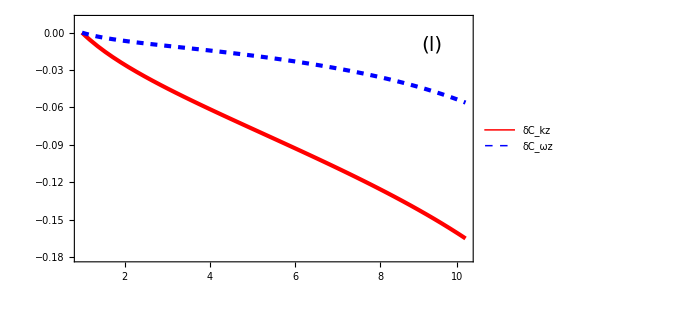

```mathematica
DL=Plot[{CkZs[τ]/CkZsnf[τ]-1,CwZs[τ]/CwZsnf[τ]-1} ,{τ,τi,τm},PlotRange->{{1,10},{-0.18,0.01}},
PlotStyle->{style1,style40},BaseStyle->textstyle,
Frame->True,LabelStyle->textstyle,FrameStyle->Directive[Black, Thickness[0.008],14],
FrameTicks->{{None,{{0.00," 0.00",0.03},{-0.01,"",0.015},{-0.02,"",0.015},{-0.03,"",0.015},{-0.04,"",0.015},{-0.05,"-0.05",0.03},{-0.06,"",0.015},{-0.07,"",0.015},{-0.08,"",0.015},{-0.09,"",0.015},{-0.1,"-0.1",0.03},{-0.11,"",0.015},{-0.12,"",0.015},{-0.13,"",0.015},{-0.14,"",0.015},{-0.15,"-0.15",0.03},{-0.16,"",0.015},{-0.17,"",0.015}}},

{{{1.5,"",0.015},{2.,"2",0.03},{2.5,"",0.015},{3.,"3",0.03},{3.5,"",0.015},{4.,"4",0.03},{4.5,"",0.015},{5.,"5",0.03},{5.5,"",0.015},{6.,"6",0.03},{6.5,"",0.015},{7.,"7",0.03},{7.5,"",0.015},{8.,"8",0.03},{8.5,"",0.015},{9.,"9",0.03},{9.5,"",0.015},{9.8,"10",0}},{1,{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}}}},


Epilog->{Text[Style["(l)",FontSize->20],{9.2,-0.01}],Text[Style["τ [fm]",FontSize->19],{5.5,-0.21}],Rotate[Text[Style["δC_k, δC_ω",FontSize->19],{11.5,-0.075}],-90Degree]},
PlotLegends->Placed[LineLegend[{"δC_kz", "δC_ωz"},LabelStyle->textstyle],Scaled[{0.25,0.25}]],PlotRangeClipping->False,ImagePadding->{{70,70},{70,5}}]
```

```mathematica
GraphicsColumn[{GraphicsRow[{AL,BL},-103],GraphicsRow[{CL,DL},-103]
},Automatic,-63]
```

-Graphics-

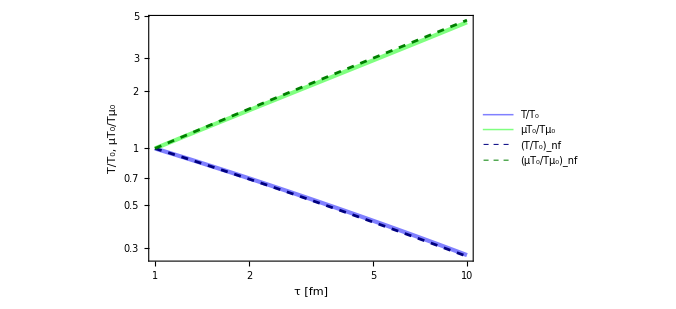

```mathematica
LogLogPlot[{Ts[τ]/Ti,μs[τ]/Ts[τ] Ti/μi,Ts0[τ]/Ti,μs0[τ]/Ts0[τ] Ti/μi},{τ,τi ,τm },
PlotStyle->{style01,style02,style010,style020},BaseStyle->textstyle,
FrameLabel->{"τ [fm]","T/T_0, μT_0/Tμ_0"},LabelStyle->textstyle,
PlotLegends->{{"T/T_0"," μT_0/Tμ_0", "(T/T_0)_nf", "(μT_0/Tμ_0)_nf"};Placed[{"T/T_0"," μT_0/Tμ_0", "(T/T_0)_nf", "(μT_0/Tμ_0)_nf"},{Right,Center}]}]
```

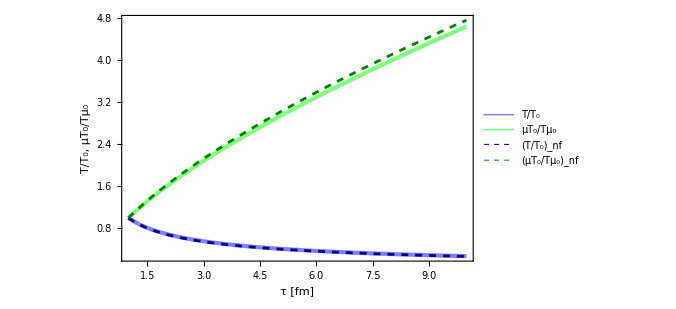

```mathematica
Plot[{Ts[τ]/Ti,μs[τ]/Ts[τ] Ti/μi,Ts0[τ]/Ti,μs0[τ]/Ts0[τ] Ti/μi},{τ,τi ,τm },
PlotStyle->{style01,style02,style010,style020},BaseStyle->textstyle,
FrameLabel->{"τ [fm]","T/T_0, μT_0/Tμ_0"},LabelStyle->textstyle,
PlotLegends->{{"T/T_0"," μT_0/Tμ_0", "(T/T_0)_nf", "(μT_0/Tμ_0)_nf"};Placed[{"T/T_0"," μT_0/Tμ_0", "(T/T_0)_nf", "(μT_0/Tμ_0)_nf"},{Right,Center}]}]
```

V. Some checks - check if contributions to densities from spin to background are small (1. Longitudinal polarization)

```mathematica
(* define function τ = τ(z) based on z=M/T=M/T(τ) *)
τz=Interpolation[Table[{M/Ts[τ],τ},{τ,τi,τm,(τm-τi)/100}]];
```

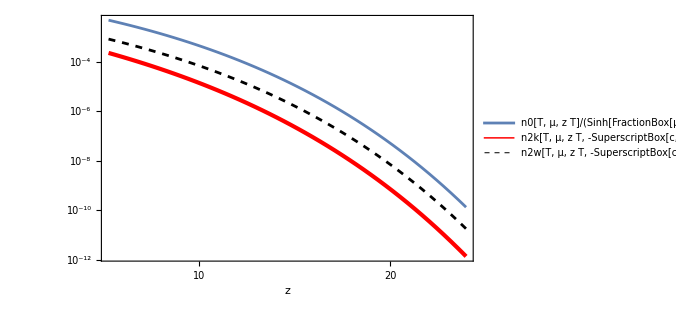

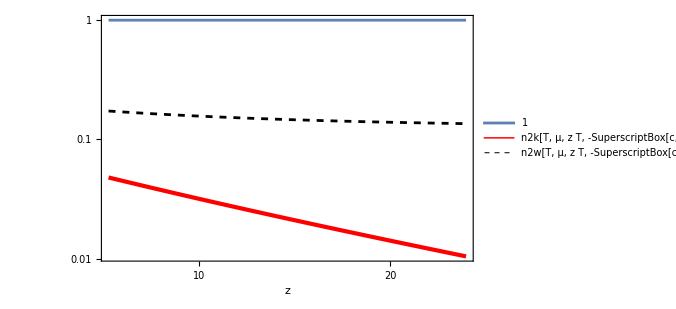

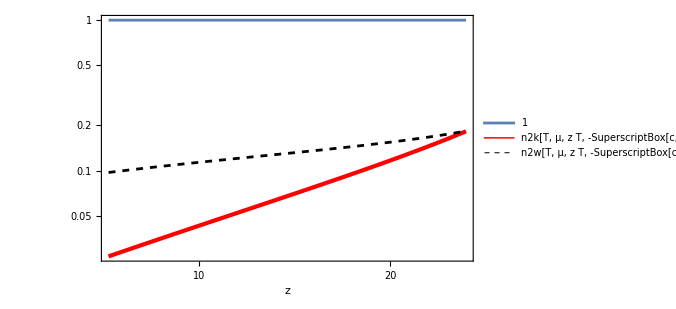

```mathematica
(* plot contributions to charge density scaled by Sinh[μ/T] T^3 and c^2 *)
LogLogPlot[{n0[T,μ,z T]/(Sinh[μ/T] T^3)//FullSimplify,n2k[T,μ,z T,-c^2]/(Sinh[μ/T] T^3 c^2)//FullSimplify,n2w[T,μ,z T,-c^2]/(Sinh[μ/T] T^3 c^2)//FullSimplify},{z,M/Ts[τi],M/Ts[τm]},
PlotStyle->{style0,style1,style2}, 
FrameLabel->{"z",""},
PlotLegends->{"n0[T, μ, z T]/(Sinh[FractionBox[μ, T]] SuperscriptBox[T, 3])","n2k[T, μ, z T, -SuperscriptBox[c, 2]]/(Sinh[FractionBox[μ, T]] SuperscriptBox[T, 3] SuperscriptBox[c, 2])","n2w[T, μ, z T, -SuperscriptBox[c, 2]]/(Sinh[FractionBox[μ, T]] SuperscriptBox[T, 3] SuperscriptBox[c, 2])"}]

LogLogPlot[{1,n2k[T,μ,z T,-c^2]/(n0[T,μ,z T] c^2)//FullSimplify,n2w[T,μ,z T,-c^2]/(n0[T,μ,z T] c^2)//FullSimplify},{z,M/Ts[τi],M/Ts[τm]},
PlotStyle->{style0,style1,style2}, 
FrameLabel->{"z",""},
PlotLegends->{"1","n2k[T, μ, z T, -SuperscriptBox[c, 2]]/(n0[T, μ, z T] SuperscriptBox[c, 2])","n2w[T, μ, z T, -SuperscriptBox[c, 2]]/(n0[T, μ, z T] SuperscriptBox[c, 2])"}]

LogLogPlot[{1, n2k[T,μ,z T,-CkZs[τz[z]]^2]/n0[T,μ,z T] //FullSimplify,n2w[T,μ,z T,-CwZs[τz[z]]^2]/n0[T,μ,z T]//FullSimplify},{z,M/Ts[τi],M/Ts[τm]},
PlotStyle->{style0,style1,style2}, 
FrameLabel->{"z",""},
PlotLegends->{"1","n2k[T, μ, z T, -SuperscriptBox[c, 2]]/n0[T, μ, z T]","n2w[T, μ, z T, -SuperscriptBox[c, 2]]/n0[T, μ, z T]"}]
```

VI. ( EVALUATE FOR solutionN=2) Solving EOMs using assumption that μ==0 and using quasi-analytic solutions to Ck and Cw; this gives single EOM for T (1. Longitudinal polarization)

```mathematica
ξ=0;
CK[τ_]= (CkZi a[Ti,ξ,M]τi)/(a[T[τ],ξ,M]τ);
CW[τ_]= (CwZi a1[Ti,ξ,M]τi)/(a1[T[τ],ξ,M]τ);
```

```mathematica
SolutionSpecial=NDSolve[{ 
Simplify[(D[eb[T[τ],0,M,-CK[τ]^2,-CW[τ]^2],τ]+1/τ(eb[T[τ],0,M,-CK[τ]^2,-CW[τ]^2]+pb[T[τ],0,M,-CK[τ]^2,-CW[τ]^2])+ps[T[τ],0,M]/τ(CK[τ]^2+CW[τ]^2)==0 )],
T[τi]==Ti
},{T},{τ,τi,τf},StartingStepSize->10^-6,Method->{"StiffnessSwitching"}][[1]];
Tss=SolutionSpecial[[1,2]]; 
τm=Tss[[1,1,2]];
```

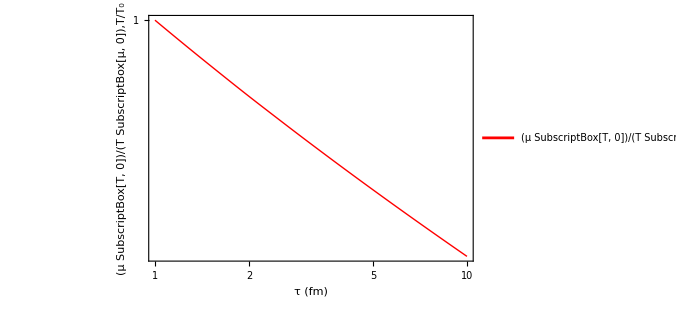

```mathematica
LogLogPlot[{ Tss[τ]/Ti},{τ,τi ,τm},PlotStyle->{{Red,Thick},{Darker[Black,0.5],Dashed}},
FrameLabel->{Style["τ (fm)",FontSize->14,Bold],Style["(μ SubscriptBox[T, 0])/(T SubscriptBox[μ, 0]),T/T_0",FontSize->14,Bold]},PlotLegends->{" (μ SubscriptBox[T, 0])/(T SubscriptBox[μ, 0])"," T/T_0"},LabelStyle->{FontSize->14,Darker[Black,0.1], Plain},PlotRange->All,Frame->True,FrameStyle ->Directive[14],Axes->False,ImageSize->500]
```

VIII. ( EVALUATE FOR solutionN=2) Solving EOMs using asymptotic expressions  in z (this is to be used with solutionN=2  (see section II) --  it should make NDSolve stop before τf)

```mathematica
ξ=0;
CK[τ_]= (CkZi a[Ti,ξ,M]τi)/(a[T[τ],ξ,M]τ);
CW[τ_]= (CwZi a1[Ti,ξ,M]τi)/(a1[T[τ],ξ,M]τ);
```

```mathematica
SolutionSpecial=NDSolve[{ 
Simplify[(D[eb[T[τ],0,M,-CK[τ]^2,-CW[τ]^2],τ]+1/τ(eb[T[τ],0,M,-CK[τ]^2,-CW[τ]^2]+pb[T[τ],0,M,-CK[τ]^2,-CW[τ]^2])+ps[T[τ],0,M]/τ(CK[τ]^2+CW[τ]^2)==0 )],
T[τi]==Ti
},{T},{τ,τi, τf},StartingStepSize->10^-6,Method->{"StiffnessSwitching"}][[1]];
Tss=SolutionSpecial[[1,2]]; 
τm=Tss[[1,1,2]];
```

```mathematica
LogLogPlot[{ Tss[τ]/Ti},{τ,τi ,τm},PlotStyle->{{Red,Thick},{Darker[Black,0.5],Dashed}},
FrameLabel->{Style["τ (fm)",FontSize->14,Bold],Style["(μ SubscriptBox[T, 0])/(T SubscriptBox[μ, 0]),T/T_0",FontSize->14,Bold]},PlotLegends->{" (μ SubscriptBox[T, 0])/(T SubscriptBox[μ, 0])"," T/T_0"},LabelStyle->{FontSize->14,Darker[Black,0.1], Plain},PlotRange->All,Frame->True,FrameStyle ->Directive[14],Axes->False,ImageSize->500]
```

-Graphics-

```mathematica
(* below I was checking what happens *)
Clear[CK,CW]
subCWdot={ CW'[τ]-> -(D[a1[T[τ],0,m ],τ]/a1[T[τ],0,m ] +1/τ) CW[τ]}/.m-> z T[τ]//FullSimplify
```

{CW'[τ]→CW[τ] (-1/τ-((z (10+z^2) BesselK[1,z]+5 (8+z^2) BesselK[2,z]) T'[τ])/(z (z BesselK[2,z]+2 BesselK[3,z]) T[τ]))}

```mathematica
(* LHS of equation solved in SolutionSpecial above; I just use xi=0 and CK=0 for simplicity, substitute CW'[τ] and CW[τ], this gives equation for T[τ] *)
lhseq=Collect[(1/(T[τ]^4/(4 π^2 z τ))(D[eb[T[τ],0,m,0,-CW[τ]^2],τ]+1/τ(eb[T[τ],0,m,0,-CW[τ]^2]+pb[T[τ],0,m,0,-CW[τ]^2])+ps[T[τ],0,m]/τ(0+(CW[τ])^2)//FullSimplify) /.subCWdot/.CW[τ]-> CWi/(a1[T[τ],0,z T[τ]]τ))/.m-> z T[τ]  ,{T'[τ]},FullSimplify]
```

4 BesselK[3,z] (2 z^4-(CWi^2 π^4 (8+z^2))/((z τ BesselK[2,z]+2 τ BesselK[3,z])^2 T[τ]^6))+((4 CWi^2 π^4 (-2 z^2 (40+15 z^2+z^4) BesselK[1,z]^2-z (640+200 z^2+13 z^4) BesselK[1,z] BesselK[2,z]+(8+z^2) (-160-20 z^2+z^4) BesselK[2,z]^2))/(z^2 τ (z BesselK[2,z]+2 BesselK[3,z])^3 T[τ]^7)+(8 z^3 τ (3 z BesselK[1,z]+(12+z^2) BesselK[2,z]))/T[τ]) T'[τ]

```mathematica
(* then we may expand for large z, keeping terms up to first nontrivial with CWi *)
lhseq2=Collect[Series[lhseq,{z,∞,-1}]//Normal,{T'[τ]},FullSimplify]
```

1/16 ⅇ^-z √(π/2) z^(3/2) (945+16 z (35+8 z))+(ⅇ^-z √(π/2) z^(3/2) (-1024 CWi^2 ⅇ^(2 z) π^3+(22365+8 z (1785+16 z (39+8 z))) τ^2 T[τ]^6) T'[τ])/(128 τ T[τ]^7)

```mathematica
(* then we may solve for T'[τ] *)
(* numerator is always positive, in denominator -1024 CWi^2 ⅇ^(2 z) π^3 is negative and (22365+8 z (1785+16 z (39+8 z))) τ^2 T[τ]^6 is positive, hence the denominator will change sign for certain set of parameters *)
rhseq=( Solve[lhseq2==0,T'[τ]]⟦1,1,2⟧ )/T[τ] //FullSimplify
```

-(8 (945+16 z (35+8 z)) τ T[τ]^6)/(-1024 CWi^2 ⅇ^(2 z) π^3+(22365+8 z (1785+16 z (39+8 z))) τ^2 T[τ]^6)

```mathematica
Solve[-1024 CWi^2 ⅇ^(2 z) π^3+(22365+8 z (1785+16 z (39+8 z))) τ^2 T[τ]^6==0/.z-> m/T[τ]//FullSimplify,CWi]
```

{{CWi→-(ⅇ^(-m/T[τ]) τ T[τ]^(3/2) √(1024 m^3+4992 m^2 T[τ]+14280 m T[τ]^2+22365 T[τ]^3))/(32 π^(3/2))},{CWi→(ⅇ^(-m/T[τ]) τ T[τ]^(3/2) √(1024 m^3+4992 m^2 T[τ]+14280 m T[τ]^2+22365 T[τ]^3))/(32 π^(3/2))}}

NDSolve::ndsz: At τ == 3.39039, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At τ == 1.5139, step size is effectively zero; singularity or stiff system suspected.

{T→InterpolatingFunction[…]}

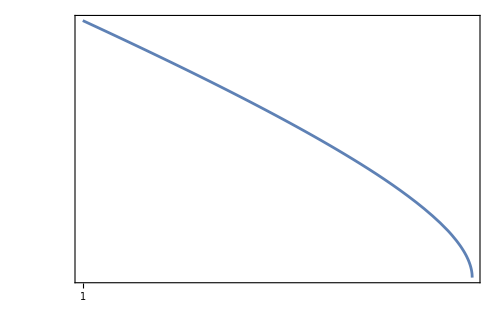
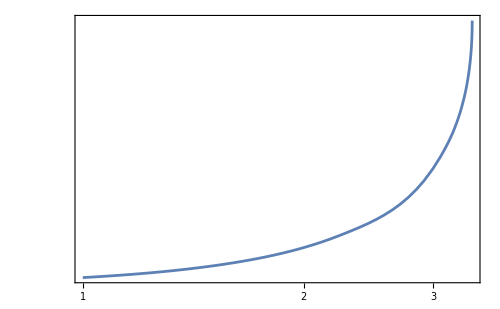

```mathematica
SolutionDecay=NDSolve[{ 
(T'[τ]/T[τ])==rhseq/.CWi-> 10^-2/.z-> M/T[τ],
T[τi]==Ti
},{T},{τ,τi,τf},StartingStepSize->10^-6,Method->{"StiffnessSwitching"}][[1]];

SolutionRiseup=NDSolve[{ 
(T'[τ]/T[τ])==rhseq/.CWi-> 10^-3/.z-> M/T[τ],
T[τi]==Ti
},{T},{τ,τi,τf},StartingStepSize->10^-6,Method->{"StiffnessSwitching"}][[1]]
Tsd=SolutionDecay[[1,2]];
Tsr=SolutionRiseup[[1,2]]; 
{LogLogPlot[{Tsr[t]},{t,τi,SolutionRiseup[[1,2,1,1,2]] }],LogLogPlot[{Tsd[t]},{t,τi,SolutionDecay[[1,2,1,1,2]] }]}
```

VII.  (EVALUATE ONLY if Ts1 and Ts2 were generated with solutionN -> see sections II and III) Some comparisons

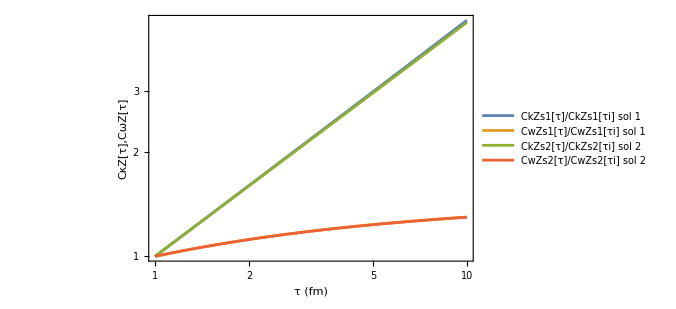
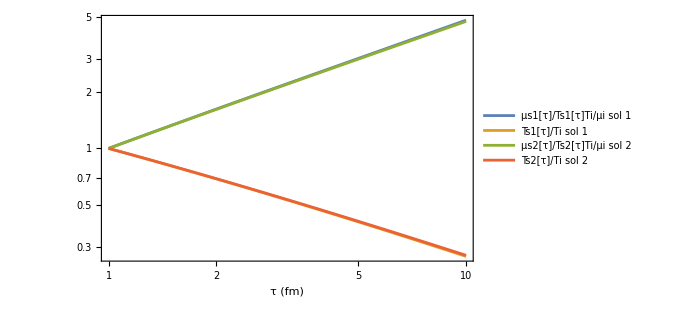

```mathematica
If[ValueQ[Ts1]&&ValueQ[Ts2],{
τm=Min[ Ts1[[1,1,2]],Ts2[[1,1,2]]];
LogLogPlot[{CkZs1[τ]/CkZs1[τi],CwZs1[τ]/CwZs1[τi],CkZs2[τ]/CkZs2[τi],CwZs2[τ]/CwZs2[τi]},{τ,τi,τm},PlotStyle->{style50,style60,style51,style61 },
FrameLabel->{Style["τ (fm)",FontSize->14,Bold],Style[" CκZ[τ],CωZ[τ]",FontSize->14]},PlotLegends->{" CkZs1[τ]/CkZs1[τi] sol 1"," CwZs1[τ]/CwZs1[τi] sol 1"," CkZs2[τ]/CkZs2[τi] sol 2"," CwZs2[τ]/CwZs2[τi] sol 2"},LabelStyle->{FontSize->14, Plain},PlotRange->All,Frame->True,FrameStyle ->Directive[14],Axes->False,ImageSize->500]


LogLogPlot[{μs1[τ]/Ts1[τ] Ti/μi,Ts1[τ]/Ti,μs2[τ]/Ts2[τ] Ti/μi,Ts2[τ]/Ti},{τ,τi,τm},PlotStyle->{style50,style60,style51,style61 },
FrameLabel->{Style["τ (fm)",FontSize->14,Bold],Style[" ",FontSize->14]},PlotLegends->{" μs1[τ]/Ts1[τ]Ti/μi sol 1"," Ts1[τ]/Ti sol 1"," μs2[τ]/Ts2[τ]Ti/μi sol 2","Ts2[τ]/Ti sol 2"},LabelStyle->{FontSize->14, Plain},PlotRange->All,Frame->True,FrameStyle ->Directive[14],Axes->False,ImageSize->500]
}]
```

VIII. Solving EOM (2. Transverse polarization)

```mathematica
(* SolutionFull contains the Bjorken solution for Ckx=Cx, Cky=Cy and Cwx=λCkx=λCx, Cwy=λCky=λCy as well as T and μ with 2nd order contributions from spin *)
TSolutionFull=NDSolve[{
D[nb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cky[τ]^2],τ]+nb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cky[τ]^2]/τ==0,
D[eb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cky[τ]^2],τ]+1/τ(eb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cky[τ]^2]+pb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cky[τ]^2])==0,
D[Ckx[τ],τ]==-1/a[T[τ],μ[τ],M](D[a[T[τ],μ[τ],M],τ]+(a[T[τ],μ[τ],M]+1/2 a[T[τ],μ[τ],M])/τ)Ckx[τ],D[Cky[τ],τ]==-1/a[T[τ],μ[τ],M](D[a[T[τ],μ[τ],M],τ]+(a[T[τ],μ[τ],M]+1/2 a[T[τ],μ[τ],M])/τ)Cky[τ],
D[Cwx[τ],τ]==-1/a1[T[τ],μ[τ],M](D[a1[T[τ],μ[τ],M],τ]+(a1[T[τ],μ[τ],M]-1/2 a[T[τ],μ[τ],M])/τ)Cwx[τ],
D[Cwy[τ],τ]==-1/a1[T[τ],μ[τ],M](D[a1[T[τ],μ[τ],M],τ]+(a1[T[τ],μ[τ],M]-1/2 a[T[τ],μ[τ],M])/τ)Cwy[τ],
T[τi]==Ti,
μ[τi]==μi,
Ckx[τi]==Ckxi,
Cky[τi]==Ckyi,
Cwx[τi]==Cwxi,
Cwy[τi]==Cwyi
},{T,μ,Ckx,Cky,Cwx,Cwy},{τ,τi,τf}, Method->{"EquationSimplification"->"Residual"}][[1]];

(* here I pick up solutions from SolutionFull, suffix _st stands for solution *)
Tst=TSolutionFull[[1,2]];
μst=TSolutionFull[[2,2]]; 
Ckxst=TSolutionFull[[3,2]]; 
Ckyst=TSolutionFull[[4,2]];
Cwxst=TSolutionFull[[5,2]];
Cwyst=TSolutionFull[[6,2]];
(* here using solutionN I pick up various solutions from SolutionFull to make comparisons *)
Switch[solutionN,
1,{
Tst1=TSolutionFull[[1,2]];
μst1=TSolutionFull[[2,2]]; 
Ckxst1=TSolutionFull[[3,2]]; 
Ckyst1=TSolutionFull[[4,2]];
Cwxst1=TSolutionFull[[5,2]];
Cwyst1=TSolutionFull[[6,2]];
},
2,{
Tst2=TSolutionFull[[1,2]];
μst2=TSolutionFull[[2,2]]; 
Ckxst2=TSolutionFull[[3,2]]; 
Ckyst2=TSolutionFull[[4,2]];
Cwxst2=TSolutionFull[[5,2]];
Cwyst2=TSolutionFull[[6,2]];
},
3,{
Tst3=TSolutionFull[[1,2]];
μst3=TSolutionFull[[2,2]]; 
Ckxst3=TSolutionFull[[3,2]]; 
Ckyst3=TSolutionFull[[4,2]];
Cwxst3=TSolutionFull[[5,2]];
Cwyst3=TSolutionFull[[6,2]];
},
4,{
Tst4=TSolutionFull[[1,2]];
μst4=TSolutionFull[[2,2]]; 
Ckxst4=TSolutionFull[[3,2]]; 
Ckyst4=TSolutionFull[[4,2]];
Cwxst4=TSolutionFull[[5,2]];
Cwyst4=TSolutionFull[[6,2]];
},
5,{
Tst5=TSolutionFull[[1,2]];
μst5=TSolutionFull[[2,2]]; 
Ckxst5=TSolutionFull[[3,2]]; 
Ckyst5=TSolutionFull[[4,2]];
Cwxst5=TSolutionFull[[5,2]];
Cwyst5=TSolutionFull[[6,2]];
},
6,{
Tst6=TSolutionFull[[1,2]];
μst6=TSolutionFull[[2,2]]; 
Ckxst6=TSolutionFull[[3,2]]; 
Ckyst6=TSolutionFull[[4,2]];
Cwxst6=TSolutionFull[[5,2]];
Cwyst6=TSolutionFull[[6,2]];
}
];

(* transverse solution for no feedback - 1st. order in Subscript[ω, μν] - calculations *)

TSolutionNF=NDSolve[{
D[nb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cwy[τ]^2],τ]+nb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cwy[τ]^2]/τ==0,
D[eb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cwy[τ]^2],τ]+(eb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cwy[τ]^2]+pb[T[τ],μ[τ],M,-Ckx[τ]^2,-Cwy[τ]^2])/τ==0,D[Ckx[τ],τ]==-1/a[T[τ],μ[τ],M](D[a[T[τ],μ[τ],M],τ]+(a[T[τ],μ[τ],M]+1/2 a[T[τ],μ[τ],M])/τ)Ckx[τ],D[Cky[τ],τ]==-1/a[T[τ],μ[τ],M](D[a[T[τ],μ[τ],M],τ]+(a[T[τ],μ[τ],M]+1/2 a[T[τ],μ[τ],M])/τ)Cky[τ],
D[Cwx[τ],τ]==-1/a1[T[τ],μ[τ],M](D[a1[T[τ],μ[τ],M],τ]+(a1[T[τ],μ[τ],M]-1/2 a[T[τ],μ[τ],M])/τ)Cwx[τ],
D[Cwy[τ],τ]==-1/a1[T[τ],μ[τ],M](D[a1[T[τ],μ[τ],M],τ]+(a1[T[τ],μ[τ],M]-1/2 a[T[τ],μ[τ],M])/τ)Cwy[τ],

T[τi]==Ti,
μ[τi]==μi,
Ckx[τi]==Ckxi,
Cky[τi]==Ckyi,
Cwx[τi]==Cwxi,
Cwy[τi]==Cwyi
},{T,μ,Ckx,Cky,Cwx,Cwy},{τ,τi,τf}, Method->{"EquationSimplification"->"Residual"}][[1]];
TsTnf=TSolutionNF[[1,2]];
μsTnf=TSolutionNF[[2,2]] ;
CkxsTnf=TSolutionNF[[3,2]];
CkysTnf=TSolutionNF[[4,2]];
CwxsTnf=TSolutionNF[[5,2]];
CwysTnf=TSolutionNF[[6,2]];

Switch[solutionN,
1,{
Tst1=TSolutionNF[[1,2]];
μst1=TSolutionNF[[2,2]]; 
Ckxst1=TSolutionNF[[3,2]]; 
Ckyst1=TSolutionNF[[4,2]];
Cwxst1=TSolutionNF[[5,2]];
Cwyst1=TSolutionNF[[6,2]];
},
2,{
Tst2=TSolutionNF[[1,2]];
μst2=TSolutionNF[[2,2]]; 
Ckxst2=TSolutionNF[[3,2]]; 
Ckyst2=TSolutionNF[[4,2]];
Cwxst2=TSolutionNF[[5,2]];
Cwyst2=TSolutionNF[[6,2]];
},
3,{
Tst3=TSolutionNF[[1,2]];
μst3=TSolutionNF[[2,2]]; 
Ckxst3=TSolutionNF[[3,2]]; 
Ckyst3=TSolutionNF[[4,2]];
Cwxst3=TSolutionNF[[5,2]];
Cwyst3=TSolutionNF[[6,2]];
},
4,{
Tst4=TSolutionNF[[1,2]];
μst4=TSolutionNF[[2,2]]; 
Ckxst4=TSolutionNF[[3,2]]; 
Ckyst4=TSolutionNF[[4,2]];
Cwxst4=TSolutionNF[[5,2]];
Cwyst4=TSolutionNF[[6,2]];
},
5,{
Tst5=TSolutionNF[[1,2]];
μst5=TSolutionNF[[2,2]]; 
Ckxst5=TSolutionNF[[3,2]]; 
Ckyst5=TSolutionNF[[4,2]];
Cwxst5=TSolutionNF[[5,2]];
Cwyst5=TSolutionNF[[6,2]];
},
6,{
Tst6=TSolutionNF[[1,2]];
μst6=TSolutionNF[[2,2]]; 
Ckxst6=TSolutionNF[[3,2]]; 
Ckyst6=TSolutionNF[[4,2]];
Cwxst6=TSolutionNF[[5,2]];
Cwyst6=TSolutionNF[[6,2]];
}
];

(* for plotting I use τm instead of τf, since sometimes the NDSolve does not reach τf *)
τm=Tst[[1,1,2]];
```

IX. Plot Solutions (2. Transverse polarization)

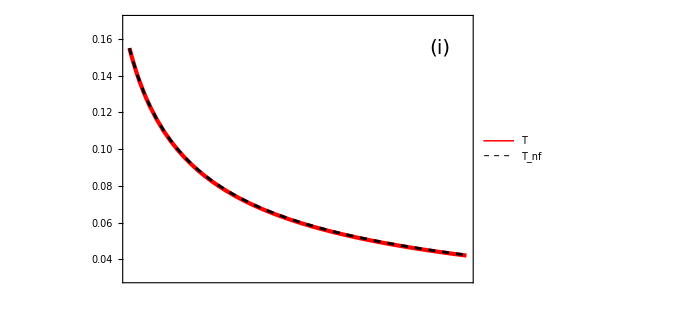

```mathematica
AT=Plot[{Tst[τ]hbarc,TsTnf[τ]hbarc},{τ,τi,τm},PlotRange->{{1,10},{0.03,0.17}},
BaseStyle->textstyle,PlotStyle->{style1,style2},
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{{{0.04,"0.04",0.03},{0.035,"",0.01},{0.045,"",0.01},{0.05,"",0.015},{0.055,"",0.01},{0.06,"0.06",0.03},{0.065,"",0.01},{0.07,"",0.015},{0.075,"",0.01},{0.08,"0.08",0.03},{0.085,"",0.01},{0.09,"",0.015},{0.095,"",0.01},{0.10,"0.10",0.03},{0.105,"",0.01},{0.11,"",0.015},{0.115,"",0.01},{0.12,"0.12",0.03},{0.125,"",0.01},{0.13,"",0.015},{0.135,"",0.01},{0.14,"0.14",0.03},{0.145,"",0.01},{0.15,"",0.015},{0.155,"",0.01},{0.16,"0.16",0.03},{0.165,"",0.01}},None},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}}}},
Epilog->{Text[Style["(i)",FontSize->20],{9.3,0.155}],Rotate[Text[Style["T [GeV]",FontSize->19],{-0.3,0.1}],90Degree]},
PlotLegends->Placed[LineLegend[{"T","T_nf"},LabelStyle->textstyle],Scaled[{0.85,0.35}]],PlotRangeClipping->False,ImagePadding->{{70,70},{70,10}}]
```

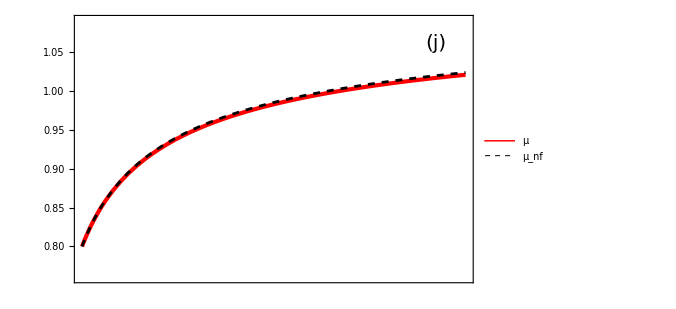

```mathematica
BT=Plot[{μst[τ]hbarc,μsTnf[τ]hbarc},{τ,τi,τm},PlotRange->{{1,10},{0.76,1.09}},
PlotStyle->{style1,style2},BaseStyle->textstyle,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{0.77,"",0.015},{0.78,"",0.015},{0.79,"",0.015},{0.80,"0.80",0.03},{0.81,"",0.015},{0.82,"",0.015},{0.83,"",0.015},{0.84,"",0.015},{0.85,"0.85",0.03},{0.86,"",0.015},{0.87,"",0.015},{0.88,"",0.015},{0.89,"",0.015},{0.9,"0.90",0.03},{0.91,"",0.015},{0.92,"",0.015},{0.93,"",0.015},{0.94,"",0.015},{0.95,"0.95",0.03},{0.96,"",0.015},{0.97,"",0.015},{0.98,"",0.015},{0.99,"",0.015},{1,"1.00",0.03},{1.01,"",0.015},{1.02,"",0.015},{1.03,"",0.015},{1.04,"",0.015},{1.05,"1.05",0.03},{1.06,"",0.015},{1.07,"",0.015},{1.08,"",0.015},{1.10,"1.10",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}}}},
Epilog->{Text[Style["(j)",FontSize->20],{9.3,1.06}],Rotate[Text[Style["μ [GeV]",FontSize->19],{11.4,0.94}],-90Degree]},
PlotLegends->Placed[LineLegend[{"μ","μ_nf"},LabelStyle->textstyle],Scaled[{0.17,0.8}]],PlotRangeClipping->False,ImagePadding->{{70,70},{70,10}}]
```

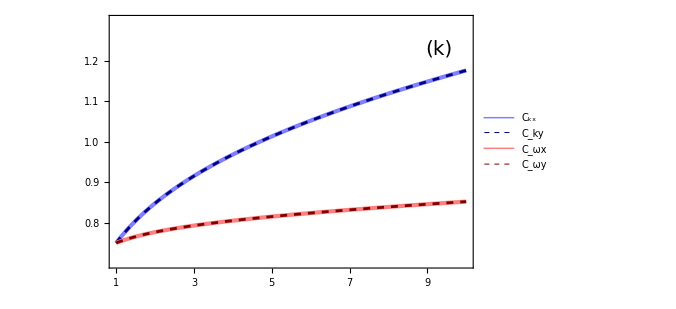

```mathematica
CT=Plot[{Ckxst[τ],Ckyst[τ],Cwxst[τ],Cwyst[τ]} ,{τ,τi,τm},PlotRange->{{1,10},{0.7,1.3}},
PlotStyle->{style01,style010,style03,style030},BaseStyle->textstyle,
Frame->True,FrameStyle->Directive[Black, Thickness[0.008],14],

FrameTicks->{{{{0.75,"",0.015},{0.8,"0.8",0.03},{0.85,"",0.015},{0.9,"0.9",0.03},{0.95,"",0.015},{1.0,"1.0",0.03},{1.05,"",0.015},{1.1,"1.1",0.03},{1.15,"",0.015},{1.2,"1.2",0.03},{1.25,"",0.015}},None},
{{1,{1.5,"",0.015},{2.,"2",0.03},{2.5,"",0.015},{3.,"3",0.03},{3.5,"",0.015},{4.,"4",0.03},{4.5,"",0.015},{5.,"5",0.03},{5.5,"",0.015},{6.,"6",0.03},{6.5,"",0.015},{7.,"7",0.03},{7.5,"",0.015},{8.,"8",0.03},{8.5,"",0.015},{9.,"9",0.03},{9.5,"",0.015},{9.8,"10",0}},{1,{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}}}},

Epilog->{Text[Style["(k)",FontSize->20],{9.3,1.23}],Text[Style["τ [fm]",FontSize->19],{5.5,0.62}],Rotate[Text[Style["C_k, C_ω",FontSize->19],{-0.08,1}],90Degree]},
PlotLegends->Placed[LineLegend[{"C_kx","C_ky","C_ωx","C_ωy"},LabelStyle->textstyle],Scaled[{0.18,0.7}]],PlotRangeClipping->False,ImagePadding->{{70,70},{70,5}}]
```

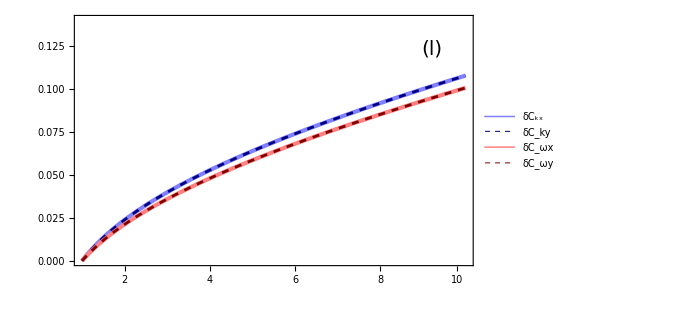

```mathematica
DL=Plot[{Ckxst[τ]/CkxsTnf[τ]-1,Ckyst[τ]/CkysTnf[τ]-1,Cwxst[τ]/CwxsTnf[τ]-1,Cwyst[τ]/CwysTnf[τ]-1} ,{τ,τi,τm},PlotRange->{{1,10},{0.0,0.14}},

PlotStyle->{style01,style010,style03,style030},BaseStyle->textstyle,PlotRange->{},
Frame->True,LabelStyle->textstyle,FrameStyle->Directive[Black, Thickness[0.008],14],
FrameTicks->{{None,{{0.01,"",0.015},{0.02,"0.02",0.03},{0.03,"",0.015},{0.04,"0.04",0.03},{0.05,"",0.015},{0.06,"0.06",0.03},{0.07,"",0.015},{0.08,"0.08",0.03},{0.08,"",0.015},{0.10,"0.10",0.03},{0.11,"",0.015},{0.12,"0.12",0.03},{0.13,"",0.015}}},

{{{1.5,"",0.015},{2.,"2",0.03},{2.5,"",0.015},{3.,"3",0.03},{3.5,"",0.015},{4.,"4",0.03},{4.5,"",0.015},{5.,"5",0.03},{5.5,"",0.015},{6.,"6",0.03},{6.5,"",0.015},{7.,"7",0.03},{7.5,"",0.015},{8.,"8",0.03},{8.5,"",0.015},{9.,"9",0.03},{9.5,"",0.015},{9.8,"10",0}},{1,{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015},{9.8,"10",0}}}},

Epilog->{Text[Style["(l)",FontSize->20],{9.2,0.123}],Text[Style["τ [fm]",FontSize->19],{5.5,-0.02}],Rotate[Text[Style["δC_k, δC_ω ",FontSize->19],{11.3,0.07}],-90Degree]},
PlotLegends->Placed[LineLegend[{"δC_kx","δC_ky","δC_ωx","δC_ωy"},LabelStyle->textstyle],Scaled[{0.2,0.7}]],PlotRangeClipping->False,ImagePadding->{{70,70},{70,5}}]
```

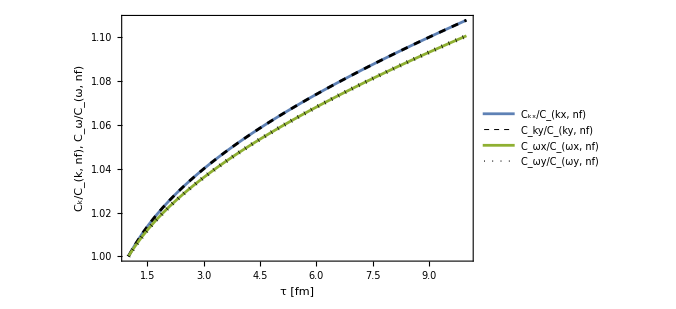

```mathematica
Plot[{Ckxst[τ]/CkxsTnf[τ],Ckyst[τ]/CkysTnf[τ],Cwxst[τ]/CwxsTnf[τ],Cwyst[τ]/CwysTnf[τ]} ,{τ,τi,τm},
PlotStyle->{style22,style2,style32,style3},BaseStyle->textstyle,
FrameLabel->{"τ [fm]","C_k/C_(k, nf),   C_ω/C_(ω, nf) "},LabelStyle->textstyle,
PlotLegends->{{"C_kx/C_(kx, nf)","C_ky/C_(ky, nf)","C_ωx/C_(ωx, nf)","C_ωy/C_(ωy, nf)"};Placed[{"C_kx/C_(kx, nf)","C_ky/C_(ky, nf)","C_ωx/C_(ωx, nf)","C_ωy/C_(ωy, nf)"},{Left,Top}]}]
```

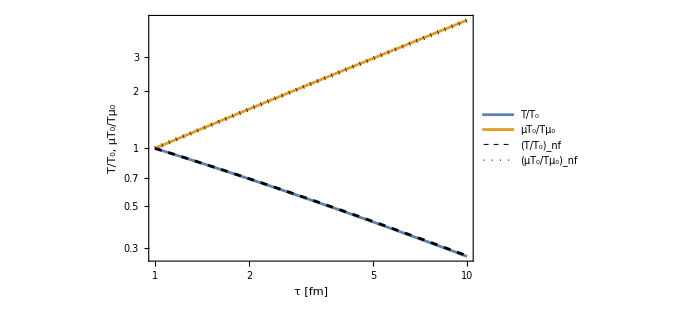

```mathematica
LogLogPlot[{Tst[τ]/Ti,μst[τ]/Tst[τ] Ti/μi,TsTnf[τ]/Ti,μsTnf[τ]/TsTnf[τ] Ti/μi},{τ,τi ,τm},
PlotStyle->{style22,style32,style2,style3},BaseStyle->textstyle,
FrameLabel->{"τ [fm]","T/T_0, μT_0/Tμ_0"},LabelStyle->textstyle,
PlotLegends->{{"T/T_0"," μT_0/Tμ_0", "(T/T_0)_nf", "(μT_0/Tμ_0)_nf"};Placed[{"T/T_0"," μT_0/Tμ_0", "(T/T_0)_nf", "(μT_0/Tμ_0)_nf"},{Right, Center}]}]
```

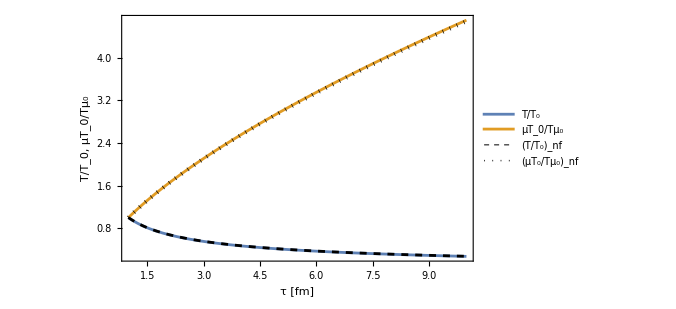

```mathematica
Plot[{Tst[τ]/Ti,μst[τ]/Tst[τ] Ti/μi,TsTnf[τ]/Ti,μsTnf[τ]/TsTnf[τ] Ti/μi},{τ,τi ,τm},
PlotStyle->{style22,style32,style2,style3},BaseStyle->textstyle,
FrameLabel->{"τ [fm]","T/T_0, μT_0/Tμ_0"},LabelStyle->textstyle,
PlotLegends->{{"T/T_0"," μT_0/Tμ_0", "(T/T_0)_nf", "(μT_0/Tμ_0)_nf"};Placed[{"T/T_0"," μT_0/Tμ_0", "(T/T_0)_nf", "(μT_0/Tμ_0)_nf"},{Right, Center}]}]
```

X. Some checks - check if contributions to densities from spin to background are small (2. Transverse polarization)

```mathematica
(* define function τ = τ(z) based on z=M/T=M/T(τ) *)
τzt=Interpolation[Table[{M/Tst[τ],τ},{τ,τi,τm,(τm-τi)/100}]];
```

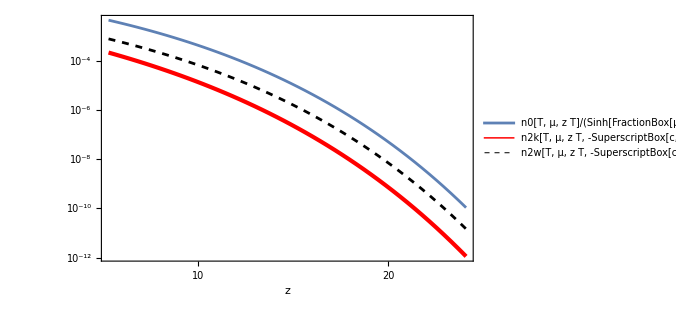

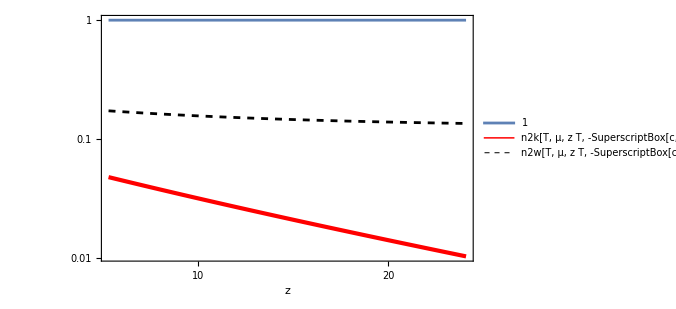

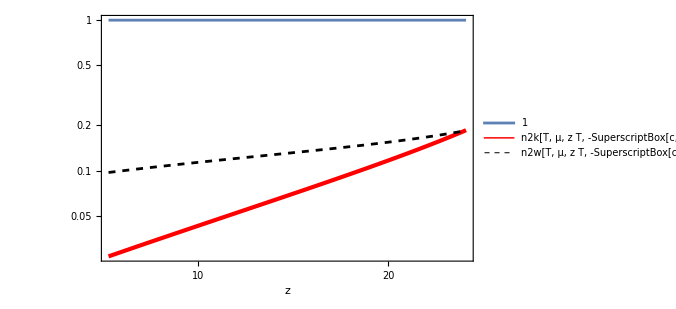

```mathematica
(* plot contributions to charge density scaled by Sinh[μ/T] T^3 and c^2 *)
LogLogPlot[{n0[T,μ,z T]/(Sinh[μ/T] T^3)//FullSimplify,n2k[T,μ,z T,-c^2]/(Sinh[μ/T] T^3 c^2)//FullSimplify,n2w[T,μ,z T,-c^2]/(Sinh[μ/T] T^3 c^2)//FullSimplify},{z,M/Tst[τi],M/Tst[τm]},
PlotStyle->{style0,style1,style2}, 
FrameLabel->{"z",""},
PlotLegends->{"n0[T, μ, z T]/(Sinh[FractionBox[μ, T]] SuperscriptBox[T, 3])","n2k[T, μ, z T, -SuperscriptBox[c, 2]]/(Sinh[FractionBox[μ, T]] SuperscriptBox[T, 3] SuperscriptBox[c, 2])","n2w[T, μ, z T, -SuperscriptBox[c, 2]]/(Sinh[FractionBox[μ, T]] SuperscriptBox[T, 3] SuperscriptBox[c, 2])"}]

LogLogPlot[{1,n2k[T,μ,z T,-c^2]/(n0[T,μ,z T] c^2)//FullSimplify,n2w[T,μ,z T,-c^2]/(n0[T,μ,z T] c^2)//FullSimplify},{z,M/Tst[τi],M/Tst[τm]},
PlotStyle->{style0,style1,style2}, 
FrameLabel->{"z",""},
PlotLegends->{"1","n2k[T, μ, z T, -SuperscriptBox[c, 2]]/(n0[T, μ, z T] SuperscriptBox[c, 2])","n2w[T, μ, z T, -SuperscriptBox[c, 2]]/(n0[T, μ, z T] SuperscriptBox[c, 2])"}]

LogLogPlot[{1, n2k[T,μ,z T,-CkZs[τz[z]]^2]/n0[T,μ,z T] //FullSimplify,n2w[T,μ,z T,-CwZs[τz[z]]^2]/n0[T,μ,z T]//FullSimplify},{z,M/Tst[τi],M/Tst[τm]},
PlotStyle->{style0,style1,style2}, 
FrameLabel->{"z",""},
PlotLegends->{"1","n2k[T, μ, z T, -SuperscriptBox[c, 2]]/n0[T, μ, z T]","n2w[T, μ, z T, -SuperscriptBox[c, 2]]/n0[T, μ, z T]"}]
```

XI. ( EVALUATE FOR solutionN=2) Solving EOMs using assumption that μ==0 and using quasi-analytic solutions to Cx and Cy; this gives single EOM for T (2. Transverse polarization)

```mathematica
ξ=0;
CX[τ_]= (Cxi a[Ti,ξ,M]τi)/(a[T[τ],ξ,M] τ^(3/2));
CY[τ_]= (Cyi a1[Ti,ξ,M]τi)/(a1[T[τ],ξ,M] τ^(3/2));
```

```mathematica
SolutionSpecialt=NDSolve[{ 
Simplify[(D[eb[T[τ],0,M,-CX[τ]^2,-CY[τ]^2],τ]+1/τ(eb[T[τ],0,M,-CX[τ]^2,-CY[τ]^2]+pb[T[τ],0,M,-CX[τ]^2,-CY[τ]^2])==0 )],
T[τi]==Ti
},{T},{τ,τi,τf},StartingStepSize->10^-6,Method->{"StiffnessSwitching"}][[1]];
Tsst=SolutionSpecialt[[1,2]]; 
τm=Tsst[[1,1,2]];
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at τ == 1..

Part::partd: Part specification 0⟦1,1,2⟧ is longer than depth of object.

```mathematica
LogLogPlot[{ Tsst[τ]/Ti},{τ,τi ,τm},PlotStyle->{{Red,Thick},{Darker[Black,0.5],Dashed}},
FrameLabel->{Style["τ (fm)",FontSize->14,Bold],Style["(μ SubscriptBox[T, 0])/(T SubscriptBox[μ, 0]),T/T_0",FontSize->14,Bold]},PlotLegends->{" (μ SubscriptBox[T, 0])/(T SubscriptBox[μ, 0])"," T/T_0"},LabelStyle->{FontSize->14,Darker[Black,0.1], Plain},PlotRange->All,Frame->True,FrameStyle ->Directive[14],Axes->False,ImageSize->500]
```

Part::partd: Part specification 0.⟦1,1,2⟧ is longer than depth of object.

Plot::plln: Limiting value 0⟦1,1,2⟧ in {τ,1.,0⟦1,1,2⟧} is not a machine-sized real number.

LogLogPlot[{Tsst[τ]/Ti},{τ,τi,τm},PlotStyle→{{Red,Thick},{Darker[Black,0.5],Dashed}},FrameLabel→{τ (fm),(μ SubscriptBox[T, 0])/(T SubscriptBox[μ, 0]),T/T_0},PlotLegends→{ (μ SubscriptBox[T, 0])/(T SubscriptBox[μ, 0]), T/T_0},LabelStyle→{FontSize→14,Darker[Black,0.1],Plain},PlotRange→All,Frame→True,FrameStyle→Directive[14],Axes→False,ImageSize→500]

```mathematica
c
```

c